```mathematica
MaximizeQ[elem_,θ_]:=Module[{m,pos},
pos=Position[elem,_Symbol];
If[MemberQ[Extract[elem, pos], θ],
m=Maximize[elem,θ];
{m[[1]],θ/.m[[2]]},
{Max[elem],0}
]
];
MinimizeQ[elem_,θ_]:=Module[{m,pos},
pos=Position[elem,_Symbol];
If[MemberQ[Extract[elem, pos], θ],
m=Minimize[elem,θ];
{m[[1]],θ/.m[[2]]},
{Min[elem],0}
]
];
```

```mathematica
boxMax[M_]:=Module[{m,val,angle},
{Max[M[[1]]],Max[M[[2]]],Max[M[[3]]]}
]
boxMax[M_,θ_]:=Module[{pos,m,val,angle},
m={Map[MaximizeQ[#,θ]&,M[[1]]],Map[MaximizeQ[#,θ]&,M[[2]]],Map[MaximizeQ[#,θ]&,M[[3]]]};
val = m[[All,All,1]];
angle = m[[All,All,2]];
pos =Map[Ordering[#]&,val][[All,-1]];
{MapThread[Part[#1,#2]&,{val,pos}],MapThread[Part[#1,#2]&,{angle,pos}]}
]
boxMin[M_]:=Module[{m,val,angle},
{ Min[M[[1]]], Min[M[[2]]], Min[M[[3]]]}
]
boxMin[M_,θ_]:=Module[{pos,m,val,angle},
m={Map[ MinimizeQ[#,θ]&,M[[1]]],Map[ MinimizeQ[#,θ]&,M[[2]]],Map[ MinimizeQ[#,θ]&,M[[3]]]};
val = m[[All,All,1]];
angle = m[[All,All,2]];
pos =Map[Ordering[#]&,val][[All,1]];
{MapThread[Part[#1,#2]&,{val,pos}],MapThread[Part[#1,#2]&,{angle,pos}]}
]
boxRange[M_]:=Module[{m,val,angle},
Transpose[{boxMin[M],boxMax[M]}]
]
boxRange[M_,θ_]:=Module[{minVal,minAng, maxVal,maxAng},
{minVal,minAng}=boxMin[M,θ];
{maxVal,maxAng}=boxMax[M,θ];
{Transpose[{minVal,maxVal}],Transpose[{minAng,maxAng}]}
]
```

The Lab color space transform is given by A.
The rotation about the L axis is given by B which is normalised to NB which preserves the -0.5 0.5 range for the a b values.

```mathematica
A[Kr_:0.299,Kb_:0.114]:={{Kr  ,(1+(-1) Kb+(-1) Kr)  ,Kb  },{(-1/2)   (1+(-1) Kb) ^(-1) Kr,(-1/2)   (1+(-1) Kb) ^(-1) (1+(-1) Kb+(-1) Kr),(1/2)  },{(1/2)  ,(-1/2) (1+(-1) Kr) ^(-1) (1+(-1) Kb+(-1) Kr)  ,(-1/2) Kb (1+(-1) Kr) ^(-1)  }};
NB [θ_:θ]:= {{1,0,0},{0,1/(Sqrt[2] Sin[θ +Pi/4])Cos[θ],1/(Sqrt[2] Sin[θ +Pi/4]) Sin[θ]},{0,-1/(Sqrt[2] Sin[θ +Pi/4]) Sin[θ],1/(Sqrt[2] Sin[θ +Pi/4]) Cos[θ]}}

B [θ_:θ]:= {{1,0,0},{0,Cos[θ], Sin[θ]},{0,- Sin[θ], Cos[θ]}}
```

```mathematica
T[θ_,Kr_:0.299,Kb_:0.114]:= FullSimplify[Chop[B[θ].A[Kr,Kb]]];
MatrixForm[T[θ,Kr,Kb]]
```

(Kr | 1-Kb-Kr | Kb
1/2 ((Kr Cos[θ])/(-1+Kb)+Sin[θ]) | -((-1+Kb+Kr) ((-1+Kr) Cos[θ]+(-1+Kb) Sin[θ]))/(2 (-1+Kb) (-1+Kr)) | 1/2 (Cos[θ]+(Kb Sin[θ])/(-1+Kr))
1/2 (Cos[θ]+(Kr Sin[θ])/(1-Kb)) | 1/2 (-1+Kb+Kr) (-Cos[θ]/(-1+Kr)+Sin[θ]/(-1+Kb)) | 1/2 ((Kb Cos[θ])/(-1+Kr)-Sin[θ]))

```mathematica
rgbcube=Table[{SurfaceColor[RGBColor[r,g,b]],Cuboid[{10.5r,10.5g,10.5b}]},{r,0,1,0.05},{g,0,1,0.05},{b,0,1,0.05}];
rgbgraph=Show[Graphics3D[rgbcube]]
```

-Graphics3D-

```mathematica
RGBCube = {{0,1,0,0,0,1,1,1},{0,0,1,0,1,0,1,1},{0,0,0,1,1,1,0,1}};
MatrixForm[RGBCube]
```

(0 | 1 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 0 | 1)

```mathematica
MatrixForm[ {boxMax[A[].RGBCube],boxMin[A[].RGBCube]}]
```

(1. | 0.5 | 0.5
0. | -0.5 | -0.5)

For A and T the range of values must lie in that given by boxRange

```mathematica
MatrixForm[ boxRange[A[].RGBCube]]
{val,ang}=boxRange[T[θ]. RGBCube,θ];
MatrixForm[val]
MatrixForm[ang]
```

(0. | 1.
-0.5 | 0.5
-0.5 | 0.5)

(0. | 1.
-0.533887 | 0.533887
-0.533887 | 0.533887)

(0 | 0
-2.24015 | 0.901447
2.47224 | -0.66935)

```mathematica
θ =0.9014465405237846;
MatrixForm[boxRange[T[θ].RGBCube]]
MatrixForm[Chop[T[θ].RGBCube]]
Clear[θ]
```

(0. | 1.
-0.533887 | 0.533887
-0.442565 | 0.442565)

(0 | 0.299 | 0.587 | 0.114 | 0.701 | 0.413 | 0.886 | 1.
0 | 0.287416 | -0.533887 | 0.246471 | -0.287416 | 0.533887 | -0.246471 | 0
0 | 0.442565 | 0 | -0.442565 | -0.442565 | 0 | 0.442565 | 0)

## Rotation Matrices

```mathematica
RotationMatrixX[α_]:={{1, 0, 0}, {0, Cos[α], Sin[α]}, {0, -Sin[α], Cos[α]}};
RotationMatrixY[β_]:={{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}};
RotationMatrixZ[γ_]:={{Cos[γ], Sin[γ], 0}, {-Sin[γ], Cos[γ], 0}, {0, 0, 1}};
R[α_,β_, γ_]:=RotationMatrixZ[γ].RotationMatrixY[β].RotationMatrixX[α]
```

```mathematica
MatrixForm[R[α,β, γ]]
```

(Cos[β] Cos[γ] | Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | -Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
-Cos[β] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]
Sin[β] | -Cos[β] Sin[α] | Cos[α] Cos[β])

Want to find the outermost rotated cube corners. 
The cube is all positive so the maximum values will be where the rotation matrix has positive values also.

```mathematica
Rot = MatrixForm[R[α,β, γ]];
RotPos = Map[Reduce[# > 0&& 0 < α < Pi/2 &&  0 < β < Pi/2 && 0 < γ < Pi/2 ,{α, β,γ},Reals,GeneratedParameters->(Subscript[c,#]&)]&,Rot,2]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

General::stop: Further output of Reduce :: nsmet will be suppressed during this calculation.

Reduce::bddom: Value Reduce`ReduceVar[1] of the domain argument should be Complexes, Reals, Algebraics, Rationals, Integers, Primes, or Automatic.

General::stop: Further output of Reduce :: bddom will be suppressed during this calculation.

Reduce[{Reduce[{Cos[β] Cos[γ],Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ],-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]}>0&&0<α<π/2&&0<β<π/2&&0<γ<π/2,{α,β,γ},Reals,GeneratedParameters→(c_#1&)],Reduce[{-Cos[β] Sin[γ],Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ],Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]}>0&&0<α<π/2&&0<β<π/2&&0<γ<π/2,{α,β,γ},Reals,GeneratedParameters→(c_#1&)],Reduce[{Sin[β],-Cos[β] Sin[α],Cos[α] Cos[β]}>0&&0<α<π/2&&0<β<π/2&&0<γ<π/2,{α,β,γ},Reals,GeneratedParameters→(c_#1&)]}>0&&0<α<π/2&&0<β<π/2&&0<γ<π/2,{α,β,γ},Reals,GeneratedParameters→(c_#1&)]

```mathematica
a11 =Reduce[Cos[β]*Cos[γ] > 0&&  -Pi/2 < β < Pi/2&& -Pi/2 < γ < Pi /2,{β,γ},Reals,GeneratedParameters->(Subscript[c,#]&)]
```

-π/2<β<π/2&&-π/2<γ<π/2

```mathematica
Reduce[Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] < 0&& -Pi < α < Pi &&  -Pi < β < Pi&& -Pi < γ < Pi ,{α, β,γ},Reals,GeneratedParameters->(Subscript[c,#]&)]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]<0&&-π<α<π&&-π<β<π&&-π<γ<π,{α,β,γ},Reals,GeneratedParameters→(c_#1&)]

```mathematica
a12a=Reduce[Cos[γ] Sin[α] Sin[β] > 0&& -Pi/2 < α < Pi/2 &&  -Pi/2 < β < Pi/2&& -Pi/2 < γ < Pi /2,{α, β,γ},Reals,GeneratedParameters->(Subscript[c,#]&)]
a12b = Reduce[Cos[α] Sin[γ] > 0&& -Pi/2 < α < Pi/2 && -Pi/2 < γ < Pi/2,{α,γ},Reals,GeneratedParameters->(Subscript[c,#]&)]
```

(-π/2<α<0&&-π/2<β<0&&-π/2<γ<π/2)||(0<α<π/2&&0<β<π/2&&-π/2<γ<π/2)

-π/2<α<π/2&&0<γ<π/2

```mathematica
RegionPlot[a12a,{α,-Pi/2, Pi/2}, {β,-Pi/2, Pi/2}]
```

-Graphics-

```mathematica
Reduce[Cos[γ] Sin[α] Sin[β] > -Cos[α] Sin[γ] && -Pi/2 < α < Pi/2 &&  -Pi/2 < β < Pi/2 && -Pi/2 < γ < 0,{α, β,γ},Reals,GeneratedParameters->(Subscript[c,#]&)]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Cos[γ] Sin[α] Sin[β]>-Cos[α] Sin[γ]&&-π/2<α<π/2&&-π/2<β<π/2&&-π/2<γ<0,{α,β,γ},Reals,GeneratedParameters→(c_#1&)]

```mathematica
Reduce[Cos[β]*Cos[γ] < 0,{β,γ},Reals]
Reduce[Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] < 0,{α, β,γ},Reals]
Reduce[-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] < 0,{α, β,γ},Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Cos[β] Cos[γ]<0,{β,γ}]

$Aborted

$Aborted

```mathematica
Solve[Cos[β]==0||Cos[γ]==0,{β,γ}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{β→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{β→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]},{γ→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{γ→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]}}

```mathematica
RotatedRGBCube[α_,β_, γ_]:={{0,Cos[β]*Cos[γ],Cos[γ]*Sin[α]*Sin[β]+Cos[α]*Sin[γ],-(Cos[α]*Cos[γ]*Sin[β])+Sin[α]*Sin[γ],Cos[γ]*(-Cos[α]+Sin[α])*Sin[β]+(Cos[α]+Sin[α])*Sin[γ],Cos[γ]*(Cos[β]-Cos[α]*Sin[β])+Sin[α]*Sin[γ],Cos[γ]*(Cos[β]+Sin[α]*Sin[β])+Cos[α]*Sin[γ],Cos[γ]*(Cos[β]+(-Cos[α]+Sin[α])*Sin[β])+(Cos[α]+Sin[α])*Sin[γ]},{0,-(Cos[β]*Sin[γ]),Cos[α]*Cos[γ]-Sin[α]*Sin[β]*Sin[γ],Cos[γ]*Sin[α]+Cos[α]*Sin[β]*Sin[γ],Cos[γ]*(Cos[α]+Sin[α])+(Cos[α]-Sin[α])*Sin[β]*Sin[γ],Cos[γ]*Sin[α]+(-Cos[β]+Cos[α]*Sin[β])*Sin[γ],Cos[α]*Cos[γ]-(Cos[β]+Sin[α]*Sin[β])*Sin[γ],Cos[γ]*(Cos[α]+Sin[α])-(Cos[β]+(-Cos[α]+Sin[α])*Sin[β])*Sin[γ]},{0,Sin[β],-(Cos[β]*Sin[α]),Cos[α]*Cos[β],Cos[β]*(Cos[α]-Sin[α]),Cos[α]*Cos[β]+Sin[β],-(Cos[β]*Sin[α])+Sin[β],Cos[β]*(Cos[α]-Sin[α])+Sin[β]}}
MatrixForm[RotatedRGBCube[α,β, γ]]
```

(0 | Cos[β] Cos[γ] | Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | -Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] | Cos[γ] (-Cos[α]+Sin[α]) Sin[β]+(Cos[α]+Sin[α]) Sin[γ] | Cos[γ] (Cos[β]-Cos[α] Sin[β])+Sin[α] Sin[γ] | Cos[γ] (Cos[β]+Sin[α] Sin[β])+Cos[α] Sin[γ] | Cos[γ] (Cos[β]+(-Cos[α]+Sin[α]) Sin[β])+(Cos[α]+Sin[α]) Sin[γ]
0 | -Cos[β] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[γ] (Cos[α]+Sin[α])+(Cos[α]-Sin[α]) Sin[β] Sin[γ] | Cos[γ] Sin[α]+(-Cos[β]+Cos[α] Sin[β]) Sin[γ] | Cos[α] Cos[γ]-(Cos[β]+Sin[α] Sin[β]) Sin[γ] | Cos[γ] (Cos[α]+Sin[α])-(Cos[β]+(-Cos[α]+Sin[α]) Sin[β]) Sin[γ]
0 | Sin[β] | -Cos[β] Sin[α] | Cos[α] Cos[β] | Cos[β] (Cos[α]-Sin[α]) | Cos[α] Cos[β]+Sin[β] | -Cos[β] Sin[α]+Sin[β] | Cos[β] (Cos[α]-Sin[α])+Sin[β])

```mathematica
MatrixForm[RotatedRGBCube[α,β, γ][[1,All]]]
MatrixForm[RotatedRGBCube[α,β, γ][[1,All]]//TrigReduce]
```

(0
Cos[β] Cos[γ]
Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]
-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
Cos[γ] (-Cos[α]+Sin[α]) Sin[β]+(Cos[α]+Sin[α]) Sin[γ]
Cos[γ] (Cos[β]-Cos[α] Sin[β])+Sin[α] Sin[γ]
Cos[γ] (Cos[β]+Sin[α] Sin[β])+Cos[α] Sin[γ]
Cos[γ] (Cos[β]+(-Cos[α]+Sin[α]) Sin[β])+(Cos[α]+Sin[α]) Sin[γ])

(0
1/2 (Cos[β-γ]+Cos[β+γ])
1/4 (Cos[α-β-γ]-Cos[α+β-γ]+Cos[α-β+γ]-Cos[α+β+γ]-2 Sin[α-γ]+2 Sin[α+γ])
1/4 (2 Cos[α-γ]-2 Cos[α+γ]+Sin[α-β-γ]-Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ])
1/4 (2 Cos[α-γ]+Cos[α-β-γ]-Cos[α+β-γ]-2 Cos[α+γ]+Cos[α-β+γ]-Cos[α+β+γ]-2 Sin[α-γ]+Sin[α-β-γ]-Sin[α+β-γ]+2 Sin[α+γ]+Sin[α-β+γ]-Sin[α+β+γ])
1/4 (2 Cos[α-γ]+2 Cos[β-γ]-2 Cos[α+γ]+2 Cos[β+γ]+Sin[α-β-γ]-Sin[α+β-γ]+Sin[α-β+γ]-Sin[α+β+γ])
1/4 (Cos[α-β-γ]+2 Cos[β-γ]-Cos[α+β-γ]+Cos[α-β+γ]+2 Cos[β+γ]-Cos[α+β+γ]-2 Sin[α-γ]+2 Sin[α+γ])
1/4 (2 Cos[α-γ]+Cos[α-β-γ]+2 Cos[β-γ]-Cos[α+β-γ]-2 Cos[α+γ]+Cos[α-β+γ]+2 Cos[β+γ]-Cos[α+β+γ]-2 Sin[α-γ]+Sin[α-β-γ]-Sin[α+β-γ]+2 Sin[α+γ]+Sin[α-β+γ]-Sin[α+β+γ]))

```mathematica
Plot[RotatedRGBCube[α,β, γ],{{α,0,Pi/2},{β,0,Pi/2}, {γ,0,Pi/2}}]
```

Plot::plln: Limiting value {β, 0, π/2} in {{α, 0, π/2}, {β, 0, π/2}, {γ, 0, π/2}} is not a machine-sized real number.

Plot[RotatedRGBCube[α,β,γ],{{α,0,π/2},{β,0,π/2},{γ,0,π/2}}]

```mathematica
RotationMatrixY[-Pi/4]. {{1/(√3)},{1/(√3)},{1/(√3)}}
RotationMatrixZ[ArcTan[1/Sqrt[2]]]. %
```

{{√(2/3)},{1/(√3)},{0}}

{{1},{0},{0}}

```mathematica
scaleMatrix = {{1/Sqrt[3],0,0},{0,Sqrt[3/2],0},{0,0,Sqrt[3/2]}};
YAB[θ_]:=scaleMatrix. RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4];
MatrixForm[FullSimplify[YAB[θ]]]
MatrixForm[FullSimplify[YAB[θ]. RGBCube]]
```

(1/3 | 1/3 | 1/3
1/2 (-Cos[θ]-√3 Sin[θ]) | Cos[θ] | 1/2 (-Cos[θ]+√3 Sin[θ])
1/2 (-√3 Cos[θ]+Sin[θ]) | -Sin[θ] | 1/2 (√3 Cos[θ]+Sin[θ]))

(0 | 1/3 | 1/3 | 1/3 | 2/3 | 2/3 | 2/3 | 1
0 | 1/2 (-Cos[θ]-√3 Sin[θ]) | Cos[θ] | 1/2 (-Cos[θ]+√3 Sin[θ]) | 1/2 (Cos[θ]+√3 Sin[θ]) | -Cos[θ] | 1/2 (Cos[θ]-√3 Sin[θ]) | 0
0 | 1/2 (-√3 Cos[θ]+Sin[θ]) | -Sin[θ] | 1/2 (√3 Cos[θ]+Sin[θ]) | 1/2 (√3 Cos[θ]-Sin[θ]) | Sin[θ] | 1/2 (-√3 Cos[θ]-Sin[θ]) | 0)

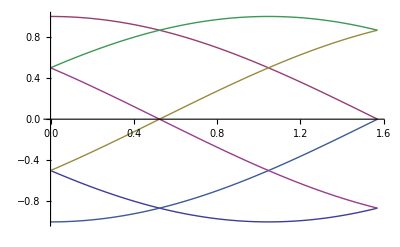

```mathematica
Plot[{1/2 (-Cos[θ]-√3 Sin[θ]),Cos[θ],1/2 (-Cos[θ]+√3 Sin[θ]),1/2 (Cos[θ]+√3 Sin[θ]),-Cos[θ],1/2 (Cos[θ]-√3 Sin[θ])},{θ,0,Pi /2}]
```

```mathematica
ACornerRanges[θ_]:= {{1/2 ( Cos[θ]-√3 Sin[θ]),1/2 (- Cos[θ]+√3 Sin[θ])},{1/2 ( Cos[θ]+√3 Sin[θ]),1/2 (- Cos[θ]-√3 Sin[θ])},{Cos[θ],-Cos[θ]}}
```

```mathematica
ACornerRanges[0]
ACornerRanges[Pi/6]
ACornerRanges[Pi/3]
ACornerRanges[Pi/2]
```

{{1/2,-1/2},{1/2,-1/2},{1,-1}}

{{0,0},{(√3)/2,-(√3)/2},{(√3)/2,-(√3)/2}}

{{-1/2,1/2},{1,-1},{1/2,-1/2}}

{{-(√3)/2,(√3)/2},{(√3)/2,-(√3)/2},{0,0}}

```mathematica
ACornerRanges[θ_]:=Piecewise[{{{Cos[θ],-Cos[θ]},θ<Pi/6 && (θ>0||θ>11Pi/6)},{{1/2 ( Cos[θ]+√3 Sin[θ]),1/2 (- Cos[θ]-√3 Sin[θ])},θ< Pi/2 && θ>Pi/6 },{{1/2 ( Cos[θ]-√3 Sin[θ]),1/2 (- Cos[θ]+√3 Sin[θ])},θ<5Pi/6 && θ>Pi/2 },{{-Cos[θ],Cos[θ]},θ<7 Pi/6 && θ>5Pi/6},{{-1/2 ( Cos[θ]+√3 Sin[θ]),1/2 ( Cos[θ]+√3 Sin[θ])},θ< 9 Pi/6 && θ>7 Pi/6 },{{-1/2 ( Cos[θ]-√3 Sin[θ]),1/2 ( Cos[θ]-√3 Sin[θ])},θ<11Pi/6 && θ>9 Pi/6 }}]
```

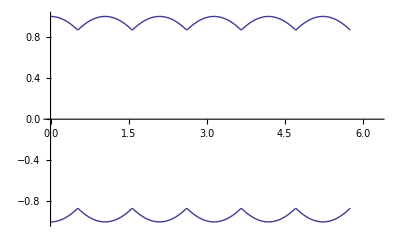

```mathematica
Plot[ACornerRanges[θ],{θ,0,2Pi }]
```

```mathematica
FCos[θ]-√3 Sin[θ]
```

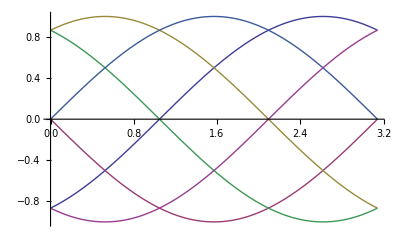

```mathematica
Plot[{1/2 (-√3 Cos[θ]+Sin[θ]),-Sin[θ],1/2 (√3 Cos[θ]+Sin[θ]),1/2 (√3 Cos[θ]-Sin[θ]),Sin[θ],1/2 (-√3 Cos[θ]-Sin[θ])},{θ,0,Pi }]
```

```mathematica
BCornerRanges[θ_]:= {{1/2 (√3 Cos[θ]-Sin[θ]),1/2 (-√3 Cos[θ]+Sin[θ])},{1/2 (√3 Cos[θ]+Sin[θ]),1/2 (-√3 Cos[θ]-Sin[θ])},{Sin[θ],-Sin[θ]}}
```

```mathematica
BCornerRanges[0]
BCornerRanges[Pi/6]
BCornerRanges[Pi/3]
BCornerRanges[Pi/2]
```

{{(√3)/2,-(√3)/2},{(√3)/2,-(√3)/2},{0,0}}

{{1/2,-1/2},{1,-1},{1/2,-1/2}}

{{0,0},{(√3)/2,-(√3)/2},{(√3)/2,-(√3)/2}}

{{-1/2,1/2},{1/2,-1/2},{1,-1}}

```mathematica
BCornerRanges[θ_]:=Piecewise[{{{1/2 (√3 Cos[θ]+Sin[θ]),1/2 (-√3 Cos[θ]-Sin[θ])},θ<Pi/3 && θ>0},{{Sin[θ],-Sin[θ]},θ<2 Pi/3 && θ>Pi/3 },{{1/2 (√3 Cos[θ]-Sin[θ]),1/2 (-√3 Cos[θ]+Sin[θ])},θ<Pi && θ>2 Pi/3 }}]
```

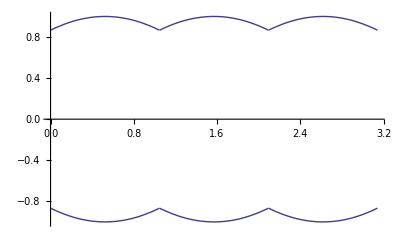

```mathematica
Plot[BCornerRanges[θ],{θ,0,Pi }]
```

```mathematica
CornerRanges[0]
```

{{0,1},{1,-1},{(√3)/2,-(√3)/2}}

```mathematica
CornerRanges[θ_]:={{0,1},{-Cos[Mod[θ-Pi/6,Pi/3]-Pi/6],Cos[Mod[θ-Pi/6,Pi/3]-Pi/6]},{-Cos[Mod[θ,Pi/3]-Pi/6],Cos[Mod[θ,Pi/3]-Pi/6]}}
```

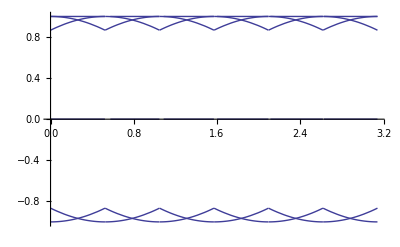

```mathematica
Plot[CornerRanges[θ],{θ,0,Pi }]
```

```mathematica
nScaleMatrix[θ_]:= {{1/Sqrt[3],0,0},{0,Sqrt[3/8]/Cos[Mod[θ-Pi/6,Pi/3]-Pi/6],0},{0,0,Sqrt[3/8]/Cos[Mod[θ,Pi/3]-Pi/6]}};
nYAB[θ_]:=FullSimplify[nScaleMatrix[θ]. RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]];
MatrixForm[nYAB[θ]]
MatrixForm[FullSimplify[nYAB[θ]]. RGBCube]
```

(1/3 | 1/3 | 1/3
-1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]) | 1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] | 1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ])
1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]) | -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ] | 1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]))

{{1/3,1/3,1/3},{-1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]),1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]],1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ])},{1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]),-1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ],1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ])}}.RGBCube

```mathematica
inYAB[θ_]:=FullSimplify[Inverse[nYAB[θ]]]
MatrixForm[inYAB[θ]]
```

(1 | -2/3 Cos[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]) | 2/3 Cos[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ])
1 | 4/3 Cos[θ] Cos[θ-1/3 π Floor[1/2+(3 θ)/π]] | -4/3 Cos[1/6 (π-6 Mod[θ,π/3])] Sin[θ]
1 | 2/3 Cos[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ]) | 2/3 Cos[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]))

```mathematica
nnYAB[θ_]:=Simplify[nScaleMatrix[θ]. RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]]
```

```mathematica
CForm[inYAB[θ]]
```

List(List(1,(-2*Cos(θ - (Pi*Floor(0.5 + (3*θ)/Pi))/3.)*(Cos(θ) + Sqrt(3)*Sin(θ)))/3.,
    (2*Cos((Pi - 6*(θ % Pi/3.))/6.)*(-(Sqrt(3)*Cos(θ)) + Sin(θ)))/3.),
   List(1,(4*Cos(θ)*Cos(θ - (Pi*Floor(0.5 + (3*θ)/Pi))/3.))/3.,(-4*Cos((Pi - 6*(θ % Pi/3.))/6.)*Sin(θ))/3.),
   List(1,(2*Cos(θ - (Pi*Floor(0.5 + (3*θ)/Pi))/3.)*(-Cos(θ) + Sqrt(3)*Sin(θ)))/3.,(2*Cos((Pi - 6*(θ % Pi/3.))/6.)*(Sqrt(3)*Cos(θ) + Sin(θ)))/3.))

```mathematica
({{1/3, 1/3, 1/3}, {-1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]), 1/2 Cos[θ] ISec[θ-1/3 π Floor[1/2+(3 θ)/π]], 1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ])}, {1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]), -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ], 1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ])}})
```

(0 | 1/3 | 1/3 | 1/3 | 2/3 | 2/3 | 2/3 | 1
0 | -1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]) | 1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] | 1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ]) | 1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]]+1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ]) | 1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ])-1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]) | 1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]]-1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]) | 1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]]+1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ])-1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ])
0 | 1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]) | -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ] | 1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]) | -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ]+1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]) | 1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ])+1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]) | -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ]+1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]) | -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ]+1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ])+1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]))

```mathematica
insm = Inverse[nScaleMatrix[θ]];
CForm[{insm[[1,1]],insm[[2,2]],insm[[3,3]]}]
```

List(Sqrt(3),2*Sqrt(0.6666666666666666)*Cos(Pi/6. - (-Pi/6. + θ) % Pi/3.),2*Sqrt(0.6666666666666666)*Cos(Pi/6. - θ % Pi/3.))

```mathematica
CForm[nYAB[θ]]
```

List(List(0.3333333333333333,0.3333333333333333,0.3333333333333333),
   List(-(Sec(θ - (Pi*Floor(0.5 + (3*θ)/Pi))/3.)*(Cos(θ) + Sqrt(3)*Sin(θ)))/4.,(Cos(θ)*Sec(θ - (Pi*Floor(0.5 + (3*θ)/Pi))/3.))/2.,
    (Sec(θ - (Pi*Floor(0.5 + (3*θ)/Pi))/3.)*(-Cos(θ) + Sqrt(3)*Sin(θ)))/4.),
   List((Sec((Pi - 6*(θ % Pi/3.))/6.)*(-(Sqrt(3)*Cos(θ)) + Sin(θ)))/4.,-(Sec((Pi - 6*(θ % Pi/3.))/6.)*Sin(θ))/2.,
    (Sec((Pi - 6*(θ % Pi/3.))/6.)*(Sqrt(3)*Cos(θ) + Sin(θ)))/4.))

```mathematica
MatrixForm[boxRange[FullSimplify[nYAB[θ]. RGBCube]]]
```

(0 | 1
Min[0,-Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]],Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]],1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]-√3 Sin[θ]),1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ]),-1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]),1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ])] | Max[0,-Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]],Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]],1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]-√3 Sin[θ]),1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ]),-1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]),1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ])]
Min[0,1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]-Sin[θ]),-Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ],Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ],1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]),-1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]),1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ])] | Max[0,1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]-Sin[θ]),-Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ],Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ],1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]),-1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]),1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ])])

```mathematica
Manipulate[Grid[{{MatrixForm[boxRange[FullSimplify[nYAB[θ]. RGBCube]]],MatrixForm[boxRange[FullSimplify[YAB[θ]. RGBCube]]],MatrixForm[CornerRanges[θ]]}}],{θ,0,Pi}]
```

Part::partw: Part 3 of YAB[2.16142] . {{0, 1, 0, 0, 0, 1, 1, 1}, {0, 0, 1, 0, 1, 0, 1, 1}, {0, 0, 0, 1, 1, 1, 0, 1}} does not exist.

Part::partw: Part 3 of nYAB[0.659734] . RGBCube does not exist.

Part::partw: Part 3 of YAB[0.659734] . RGBCube does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 3 of {{0.333333, 0.333333, 0.333333}, {-0.5, 0.426709, 0.0732908}, {-0.190685, -0.309315, 0.5}} . RGBCube does not exist.

Part::partw: Part 3 of YAB[0.659734] . RGBCube does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
MatrixForm[N[nYAB[Pi/12]]]
```

(0.333333 | 0.333333 | 0.333333
-0.366025 | 0.5 | -0.133975
-0.366025 | -0.133975 | 0.5)

```mathematica
MatrixForm[boxRange[YAB[0]. RGBCube]]
MatrixForm[boxRange[YAB[Pi/6]. RGBCube]]
MatrixForm[boxRange[YAB[Pi/4]. RGBCube]]
MatrixForm[boxRange[YAB[Pi/3]. RGBCube]]
MatrixForm[boxRange[YAB[Pi/2]. RGBCube]]
```

(0 | 1
-1 | 1
-(√3)/2 | (√3)/2)

(0 | 1
-(√3)/2 | (√3)/2
-1 | 1)

(0 | 1
-(√(3/2))/2-1/(2 √2) | (√(3/2))/2+1/(2 √2)
-(√(3/2))/2-1/(2 √2) | (√(3/2))/2+1/(2 √2))

(0 | 1
-1 | 1
-(√3)/2 | (√3)/2)

(0 | 1
-(√3)/2 | (√3)/2
-1 | 1)

```mathematica
N[√3]
```

1.73205

```mathematica
N[2 √2]
```

2.82843

```mathematica
boxRange[YAB[θ]. RGBCube,θ]
```

{{{0,1},{-1,1},{-1,1}},{{0,0},{π/3,(5 π)/3},{(11 π)/6,(7 π)/6}}}

```mathematica
CForm[YAB[θ]]
```

List(List(1/Sqrt(3),1/Sqrt(3),1/Sqrt(3)),List(-(Cos(θ)/Sqrt(6)) - Sin(θ)/Sqrt(2),Sqrt(0.6666666666666666)*Cos(θ),-(Cos(θ)/Sqrt(6)) + Sin(θ)/Sqrt(2)),
   List(-(Cos(θ)/Sqrt(2)) + Sin(θ)/Sqrt(6),-(Sqrt(0.6666666666666666)*Sin(θ)),Cos(θ)/Sqrt(2) + Sin(θ)/Sqrt(6)))

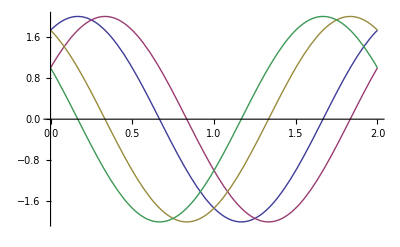

```mathematica
Plot[{√3 Cos[θ Pi]+ Sin[θ Pi],Cos[θ Pi]+√3 Sin[θ Pi],√3 Cos[θ Pi]- Sin[θ Pi],Cos[θ Pi]-√3 Sin[θ Pi]},{θ,0,2 }]
```

```mathematica
MatrixForm[RGBCube]
```

(0 | 1 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 0 | 1)

```mathematica
FullSimplify[√3 RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]]
```

{{1,1,1},{-(Cos[θ]+√3 Sin[θ])/(√2),√2 Cos[θ],(-Cos[θ]+√3 Sin[θ])/(√2)},{(-√3 Cos[θ]+Sin[θ])/(√2),-√2 Sin[θ],(√3 Cos[θ]+Sin[θ])/(√2)}}

```mathematica
FullSimplify[ArcTan[1/Sqrt[2]]/Pi]
```

ArcCot[√2]/π

```mathematica
Sin[Pi/3]
```

(√3)/2

```mathematica
RotationMatrixX[-Pi/4]. {{1/(√3)},{1/(√3)},{1/(√3)}}
RotationMatrixY[-ArcTan[Sqrt[2]]]. %
```

{{1/(√3)},{0},{√(2/3)}}

{{1},{0},{0}}

```mathematica
RotationMatrixZ[θ].RotationMatrixY[-ArcTan[Sqrt[2]]].RotationMatrixX[-Pi/4]
```

{{Cos[θ]/(√3),Cos[θ]/(√3)+Sin[θ]/(√2),Cos[θ]/(√3)-Sin[θ]/(√2)},{-Sin[θ]/(√3),Cos[θ]/(√2)-Sin[θ]/(√3),-Cos[θ]/(√2)-Sin[θ]/(√3)},{-√(2/3),1/(√6),1/(√6)}}

```mathematica
RotationMatrixX[Pi/4]. {{1/(√3)},{1/(√3)},{1/(√3)}}
RotationMatrixY[-ArcTan[1/(√2)]]. %
```

{{1/(√3)},{√(2/3)},{0}}

{{(√2)/3},{√(2/3)},{-1/3}}

```mathematica
N[ArcCos[√3]]
N[ArcSin[√3]]
```

0.+1.14622 ⅈ

1.5708-1.14622 ⅈ

```mathematica
RotationMatrixY[θ]
```

{{Cos[θ],0,-Sin[θ]},{0,1,0},{Sin[θ],0,Cos[θ]}}

```mathematica
RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]
```

{{1/(√3),1/(√3),1/(√3)},{-1/(√6),√(2/3),-1/(√6)},{-1/(√2),0,1/(√2)}}

```mathematica
RotationMatrixZ[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]
```

{{(√(2/3) Cos[θ]-Sin[θ]/(√3))/(√2),Cos[θ]/(√3)+√(2/3) Sin[θ],(√(2/3) Cos[θ]-Sin[θ]/(√3))/(√2)},{(-Cos[θ]/(√3)-√(2/3) Sin[θ])/(√2),√(2/3) Cos[θ]-Sin[θ]/(√3),(-Cos[θ]/(√3)-√(2/3) Sin[θ])/(√2)},{-1/(√2),0,1/(√2)}}

```mathematica
RotationMatrixY[-Pi/4]
RotationMatrixZ[ArcTan[1/Sqrt[2]]].%
RotationMatrixY[θ].%
```

{{1/(√2),0,1/(√2)},{0,1,0},{-1/(√2),0,1/(√2)}}

{{1/(√3),1/(√3),1/(√3)},{-1/(√6),√(2/3),-1/(√6)},{-1/(√2),0,1/(√2)}}

{{Cos[θ]/(√3)+Sin[θ]/(√2),Cos[θ]/(√3),Cos[θ]/(√3)-Sin[θ]/(√2)},{-1/(√6),√(2/3),-1/(√6)},{-Cos[θ]/(√2)+Sin[θ]/(√3),Sin[θ]/(√3),Cos[θ]/(√2)+Sin[θ]/(√3)}}

```mathematica
{{0},{(2 √2)/3},{-1/3}}
```

```mathematica
√(2/3)/(1/(√3))
```

```mathematica
ArcTan[√2
```

```mathematica
N[ArcTan[1/Sqrt[3]]]
```

0.523599

π/2-ArcTan[1/(√2)]

```mathematica
Solve[R[α,β, γ]==A[],{α,β, γ}]
```

{}

```mathematica
{{Cos[γ], Sin[γ], 0}, {-Sin[γ], Cos[γ], 0}, {0, 0, 1}}
```

```mathematica
MatrixForm[R[α,β, γ]]
MatrixForm[A[]]
```

(Cos[β] Cos[γ] | Cos[β] Sin[γ] | -Sin[β]
Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ] | Cos[α] Cos[γ]+Sin[α] Sin[β] Sin[γ] | Cos[β] Sin[α]
Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] | -Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[β])

(0.299 | 0.587 | 0.114
-0.168736 | -0.331264 | 1/2
1/2 | -0.418688 | -0.0813124)

```mathematica
Conditions=MapThread[(#1==#2)&,{Flatten[R[α,β, γ]],Flatten[A[1/3,1/3]]}];
MatrixForm[Conditions]
```

(Cos[β] Cos[γ]==1/3
Cos[β] Sin[γ]==1/3
-Sin[β]==1/3
Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]==-1/4
Cos[α] Cos[γ]+Sin[α] Sin[β] Sin[γ]==-1/4
Cos[β] Sin[α]==1/2
Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]==1/2
-Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]==-1/4
Cos[α] Cos[β]==-1/4)

```mathematica
N[Reduce[-Sin[β]==1/(√3),{β}]]
```

C[1]∈Integers&&(β==-0.61548+6.28319 C[1]||β==3.75707+6.28319 C[1])

```mathematica
-0.6154797086703874/Pi
```

-0.195913

```mathematica
Conditions/. {β->-0.11424837933153527}
```

{0.993481 Cos[γ]==0.299,0.993481 Sin[γ]==0.587,True,-0.114 Cos[γ] Sin[α]-Cos[α] Sin[γ]==-0.168736,Cos[α] Cos[γ]-0.114 Sin[α] Sin[γ]==-0.331264,0.993481 Sin[α]==1/2,-0.114 Cos[α] Cos[γ]+Sin[α] Sin[γ]==1/2,-Cos[γ] Sin[α]-0.114 Cos[α] Sin[γ]==-0.418688,0.993481 Cos[α]==-0.0813124}

```mathematica
Solve[0.9934807496876826 Sin[γ]==0.587 ,γ]
Solve[0.9934807496876826 Cos[γ]==0.299,γ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{γ→0.632114}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{γ→-1.2651},{γ→1.2651}}

```mathematica
Conditions/. {β->-0.11424837933153527,γ->0.6321143732471498}
```

{False,True,True,-0.590852 Cos[α]-0.0919729 Sin[α]==-0.168736,0.80678 Cos[α]-0.0673571 Sin[α]==-0.331264,0.993481 Sin[α]==1/2,-0.0919729 Cos[α]+0.590852 Sin[α]==1/2,-0.0673571 Cos[α]-0.80678 Sin[α]==-0.418688,0.993481 Cos[α]==-0.0813124}

```mathematica
RotationMatrix[{{1,1,1}, {√3,0,0}}]
```

{{1/(√3),1/(√3),1/(√3)},{-1/(√3),1/6 (3+√3),1/6 (-3+√3)},{-1/(√3),1/6 (-3+√3),1/6 (3+√3)}}

```mathematica
MatrixForm[Map[FullSimplify[#]&,RotationMatrixX[α]. RotationMatrix[{{1,1,1}, {1,0,0}}],2]]
CForm[%]
```

(1/(√3) | 1/(√3) | 1/(√3)
-(Cos[α]+Sin[α])/(√3) | 1/6 ((3+√3) Cos[α]+(-3+√3) Sin[α]) | 1/6 ((-3+√3) Cos[α]+(3+√3) Sin[α])
(-Cos[α]+Sin[α])/(√3) | 1/6 ((-3+√3) Cos[α]-(3+√3) Sin[α]) | 1/6 ((3+√3) Cos[α]-(-3+√3) Sin[α]))

List(List(1/Sqrt(3),1/Sqrt(3),1/Sqrt(3)),List(-((Cos(α) + Sin(α))/Sqrt(3)),((3 + Sqrt(3))*Cos(α) + (-3 + Sqrt(3))*Sin(α))/6.,
    ((-3 + Sqrt(3))*Cos(α) + (3 + Sqrt(3))*Sin(α))/6.),List((-Cos(α) + Sin(α))/Sqrt(3),((-3 + Sqrt(3))*Cos(α) - (3 + Sqrt(3))*Sin(α))/6.,
    ((3 + Sqrt(3))*Cos(α) - (-3 + Sqrt(3))*Sin(α))/6.))

```mathematica
MatrixForm[A[]]
```

(0.299 | 0.587 | 0.114
-0.168736 | -0.331264 | 1/2
1/2 | -0.418688 | -0.0813124)

```mathematica
MatrixForm[A[1/3,1/3]]
```

(1/3 | 1/3 | 1/3
-1/4 | -1/4 | 1/2
1/2 | -1/4 | -1/4)